## 疑似bug

### 1. 下面的极坐标绘图有问题，曲线应该重合才对！

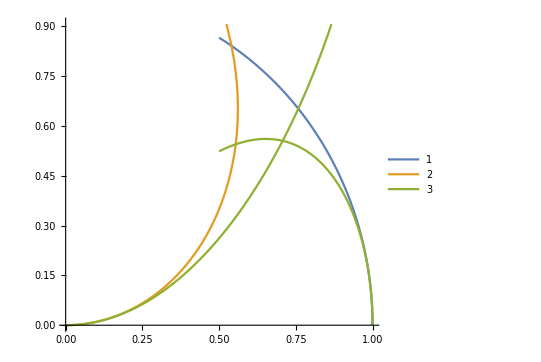

```mathematica
f  = E^(I w);
PolarPlot[{Abs[f],Arg[f], AbsArg[f]},{w,0,Pi/3},PlotLegends->Automatic]
```